```mathematica
f1[x_] := x
```

```mathematica
f2[x_] := 3 - x
```

```mathematica
f3[x_] := Sin[x]
```

```mathematica
alpha = -0.4
```

```mathematica
-0.4
```

```mathematica
g[x_] = ( f1[x]*Exp[alpha*f1[x]] + f2[x]*Exp[alpha*f2[x]] + f3[x]*Exp[alpha*f3[x]] )/( Exp[alpha*f1[x]] + Exp[alpha*f2[x]] + Exp[alpha*f3[x]] )
```

(ⅇ^(-0.4 (3-x)) (3-x)+ⅇ^(-0.4 x) x+ⅇ^(-0.4 Sin[x]) Sin[x])/(ⅇ^(-0.4 (3-x))+ⅇ^(-0.4 x)+ⅇ^(-0.4 Sin[x]))

```mathematica
(ⅇ^(2 x) x+ⅇ^(2 x^2) x^2+ⅇ^(2 Sin[x]) Sin[x])/(ⅇ^(2 h1[x])+ⅇ^(2 h2[x])+ⅇ^(2 h3[x]))
g[1]
```

(ⅇ^(2 x) x+ⅇ^(2 x^2) x^2+ⅇ^(2 Sin[x]) Sin[x])/(ⅇ^(2 h1[x])+ⅇ^(2 h2[x])+ⅇ^(2 h3[x]))

1.18328

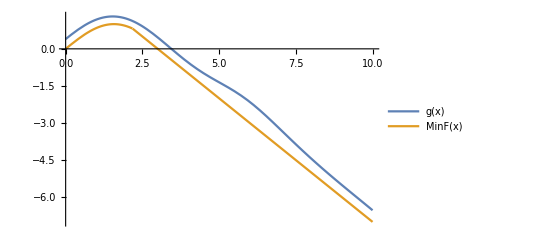

```mathematica
Plot[{g[x],MinF[x]},{x,0,10},PlotLegends->"Expressions"]
```

```mathematica
MinF[x_] = Min[f1[x],f2[x],f3[x]]
```

Min[3-x,x,Sin[x]]

```mathematica
Plot[Min[f1[x],f2[x],f3[x]],{x,0,10}]
```

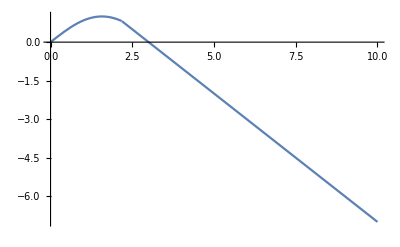

```mathematica
m[x_] = Grad[g[x],{x}]
```

{-(((0.4 ⅇ^(-0.4 (3-x))-0.4 ⅇ^(-0.4 x)-0.4 ⅇ^(-0.4 Sin[x]) Cos[x]) (ⅇ^(-0.4 (3-x)) (3-x)+ⅇ^(-0.4 x) x+ⅇ^(-0.4 Sin[x]) Sin[x]))/(ⅇ^(-0.4 (3-x))+ⅇ^(-0.4 x)+ⅇ^(-0.4 Sin[x]))^2)+(-ⅇ^(-0.4 (3-x))+ⅇ^(-0.4 x)+0.4 ⅇ^(-0.4 (3-x)) (3-x)-0.4 ⅇ^(-0.4 x) x+ⅇ^(-0.4 Sin[x]) Cos[x]-0.4 ⅇ^(-0.4 Sin[x]) Cos[x] Sin[x])/(ⅇ^(-0.4 (3-x))+ⅇ^(-0.4 x)+ⅇ^(-0.4 Sin[x]))}

```mathematica
m[1]
```

{0.466542}

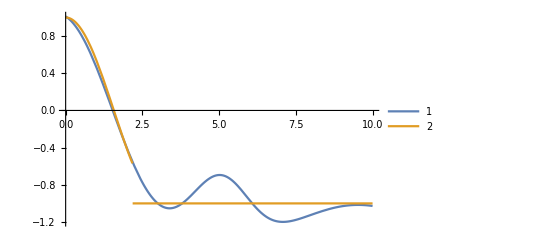

```mathematica
Plot[{m[x],MinFgrad[x]},{x,0,10},PlotLegends->Automatic]
```

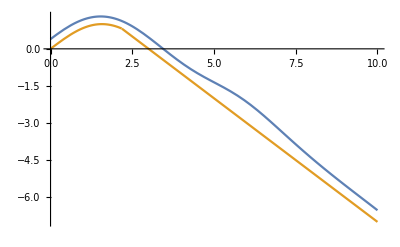

```mathematica
m[1]
```

{0.466542}

```mathematica
MinFgrad[x_] = Grad[MinF[x],{x}]
```

{Piecewise[{{-1, x≥3/2&&x+Sin[x]≥3}, {1, x<3/2&&x-Sin[x]≤0}, {Cos[x], True}}]}

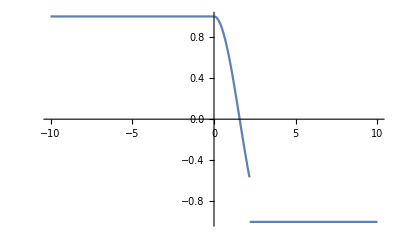

```mathematica
Plot[MinFgrad[x],{x,-10,10}]
```

```mathematica
g2[f1_,f2_,f3_,x_] = ( f1[x]*Exp[alpha*f1[x]] + f2[x]*Exp[alpha*f2[x]] + f3[x]*Exp[alpha*f3[x]] )/( Exp[alpha*f1[x]] + Exp[alpha*f2[x]] + Exp[alpha*f3[x]] )
```

(ⅇ^(-0.4 (3-x)) (3-x)+ⅇ^(-0.4 x) x+ⅇ^(-0.4 Sin[x]) Sin[x])/(ⅇ^(-0.4 (3-x))+ⅇ^(-0.4 x)+ⅇ^(-0.4 Sin[x]))

```mathematica
gF1[x_] = Grad[g2[f1,f2,f3,x],{f1,f2,f3}]
```

Set::write: Tag List in {g2'[f1]}[x_] is Protected.

{0}